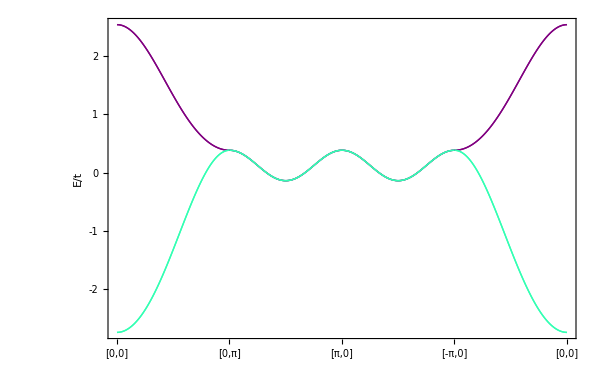

```mathematica
Vddπ =1.0; Vddσ = -1.5; Vddδ =- 0.25;  θ=(10Pi/180);Vddπ2 =1.0; Vddσ2 = -1.5; Vddδ2 = -0.25;    
Vddπn = 1.0*0.07; Vddσn = -1.5*0.07; Vddδn = -0.25*0.07; 
ϵ00[θ_,kx_,ky_]:=(4/3(Vddπ2+Vddδ2)+(4Vddπ2+ (Vddδ2-4 Vddπ2+3 Vddσ2) Cos[2 θ]^2)/3) Cos[kx]Cos[ky];
ϵnn[θ_,kx_,ky_]:=(2/3(Vddδn+Vddπn)+(Vddδn+4 Vddπn+3 Vddσn-(Vddδn-4 Vddπn+3 Vddσn) Cos[4 θ])(1/12)
)( Cos[2kx]+Cos[2ky]);
ϵa[θ_,kx_,ky_]:=(2/3 (Vddδ+Vddπ) Cos[2 θ]+(1/12)(-Vddδ+12 Vddπ-3 Vddσ+(Vddδ-4 Vddπ+3 Vddσ) Cos[4 θ]))(Cos[kx]+Cos[ky]);
ϵ1d[θ_,kx_,ky_]:=(2/3 (Vddπ+Vddδ) Sin[2θ]) (Cos[kx]+Cos[ky]);


isb2[θ_,kx_,ky_]:=({{ϵ00[θ,kx,ky]+ϵnn[θ,kx,ky], ϵa[θ,kx,ky]-I ϵ1d[θ,kx,ky], 0, 0}, {ϵa[θ,kx,ky]+I ϵ1d[θ,kx,ky], ϵ00[θ,kx,ky]+ϵnn[θ,kx,ky], 0, 0}, {0, 0, ϵ00[θ,kx,ky]+ϵnn[θ,kx,ky], ϵa[θ,kx,ky]+I ϵ1d[θ,kx,ky]}, {0, 0, ϵa[θ,kx,ky]-I ϵ1d[θ,kx,ky], ϵ00[θ,kx,ky]+ϵnn[θ,kx,ky]}});

h[θ_,kx_,ky_]:=N[isb2[θ,kx,ky]];



div=100;
(*(*kx=0-> Pi, ky=0*)
mc2D1=Table[0,{i,1,101}];
For[i=0,i≤Pi,i=i+Pi/div,
j=0;
mc2D1[[Simplify[(i)(div/(Pi))+1]]]=h[i,j];
]
u2D1=Table[0,{i,1,101}];
For[i=1,i≤101,i++,
u2D1[[i]]={Simplify[(i-1)(Pi/div)],0,Sort[Re[Eigenvalues[mc2D1⟦i⟧]],Greater]}
]
data2D1=Table[Table[{u2D1[[i]][[1]],u2D1[[i]][[3]][[j]]},{i,1,101}],{j,1,6}];*)
(*kx= -Pi -> Pi, ky = 0, (θ, ϕ) = +x *)
mc2D1=Table[0,{i,1,div+1}];
For[i=0,i≤Pi,i=i+Pi/(div),
mc2D1[[Simplify[(i)(div/(Pi))+1]]]=h[θ,i,0];
]
u2D1=Table[0,{i,1,div+1}];
For[i=1,i≤div+1,i++,
u2D1[[i]]={Simplify[(i-1)(Pi/(div))],0,Sort[Re[Eigenvalues[mc2D1⟦i⟧]],Greater]}
]
data2D1=Table[Table[{u2D1[[i]][[1]],u2D1[[i]][[3]][[j]]},{i,1,div+1}],{j,1,4}];

mc2D2=Table[0,{i,1,div+1}];
For[i=0,i≤Pi,i=i+Pi/(div),
mc2D2[[Simplify[(i)(div/(Pi))+1]]]=h[θ,Pi-i,i];
]
u2D2=Table[0,{i,1,div+1}];
For[i=1,i≤div+1,i++,
u2D2[[i]]={Pi-Simplify[(i-1)(Pi/(div))],Simplify[(i-1)(Pi/(div))],Sort[Re[Eigenvalues[mc2D2⟦i⟧]],Greater]}
]
data2D2=Table[Table[{Pi+u2D2[[i]][[2]],u2D2[[i]][[3]][[j]]},{i,1,div+1}],{j,1,4}];


mc2D3=Table[0,{i,1,div+1}];
For[i=0,i≤Pi,i=i+Pi/(div),
mc2D3[[Simplify[(i)(div/(Pi))+1]]]=h[θ,-i,Pi-i];
]
u2D3=Table[0,{i,1,div+1}];
For[i=1,i≤div+1,i++,
u2D3[[i]]={-Simplify[(i-1)(Pi/(div))],Pi-Simplify[(i-1)(Pi/(div))],Sort[Re[Eigenvalues[mc2D3⟦i⟧]],Greater]}
]
data2D3=Table[Table[{-u2D3[[i]][[1]]+2Pi,u2D3[[i]][[3]][[j]]},{i,1,div+1}],{j,1,4}];


mc2D4=Table[0,{i,1,div+1}];
For[i=0,i≤Pi,i=i+Pi/(div),
mc2D4[[Simplify[(i)(div/(Pi))+1]]]=h[θ,-Pi+i,0];
]
u2D4=Table[0,{i,1,div+1}];
For[i=1,i≤div+1,i++,
u2D4[[i]]={-Pi+Simplify[(i-1)(Pi/(div))],0,Sort[Re[Eigenvalues[mc2D4⟦i⟧]],Greater]}
]
data2D4=Table[Table[{u2D4[[i]][[1]]+4Pi,u2D4[[i]][[3]][[j]]},{i,1,div+1}],{j,1,4}];








ListPlot[{data2D1⟦1⟧,data2D1⟦2⟧,data2D1⟦3⟧,data2D1⟦4⟧,data2D2⟦1⟧,data2D2⟦2⟧,data2D2⟦3⟧,data2D2⟦4⟧,data2D3⟦1⟧,data2D3⟦2⟧,data2D3⟦3⟧,data2D3⟦4⟧,data2D4⟦1⟧,data2D4⟦2⟧,data2D4⟦3⟧,data2D4⟦4⟧},Joined->True,Frame->True,PlotStyle->{Purple,Purple,CMYKColor[0.8,0,0.3,0],CMYKColor[0.8,0,0.3,0]},FrameStyle->Directive[FontSize->30],PlotRange->All,FrameTicks->{{{2,1,0,-1,-2,-3,-4},None},{{{0,"[0,0]"},{Pi,"[0,π]"},{2Pi,"[π,0]"},{3Pi,"[-π,0]"},{4Pi,"[0,0]"}},None}},Axes->{False,False},GridLines->{{0,Pi,2Pi,3Pi,4Pi},{0.0}},FrameLabel->{None,Style["E/t",FontSize->30]},GridLinesStyle->Dashed,ImageSize->600]
```

```mathematica
data2D3⟦1⟧
```

{{π/2,-0.13945},{(101 π)/2,-0.0980291},{(201 π)/2,-0.0566},{(301 π)/2,-0.0151731},{(401 π)/2,0.0262411},{(501 π)/2,0.0676325},{(601 π)/2,0.108991},{(701 π)/2,0.150306},{(801 π)/2,0.191567},{(901 π)/2,0.232764},{(1001 π)/2,0.273887},{(1101 π)/2,0.314925},{(1201 π)/2,0.355869},{(1301 π)/2,0.396708},{(1401 π)/2,0.437431},{(1501 π)/2,0.478029},{(1601 π)/2,0.518491},{(1701 π)/2,0.558807},{(1801 π)/2,0.598967},{(1901 π)/2,0.638962},{(2001 π)/2,0.678779},{(2101 π)/2,0.718411},{(2201 π)/2,0.757846},{(2301 π)/2,0.797074},{(2401 π)/2,0.836087},{(2501 π)/2,0.874873},{(2601 π)/2,0.913423},{(2701 π)/2,0.951727},{(2801 π)/2,0.989775},{(2901 π)/2,1.02756},{(3001 π)/2,1.06507},{(3101 π)/2,1.10229},{(3201 π)/2,1.13922},{(3301 π)/2,1.17584},{(3401 π)/2,1.21216},{(3501 π)/2,1.24815},{(3601 π)/2,1.2838},{(3701 π)/2,1.31912},{(3801 π)/2,1.35409},{(3901 π)/2,1.3887},{(4001 π)/2,1.42294},{(4101 π)/2,1.4568},{(4201 π)/2,1.49028},{(4301 π)/2,1.52336},{(4401 π)/2,1.55604},{(4501 π)/2,1.58831},{(4601 π)/2,1.62016},{(4701 π)/2,1.65159},{(4801 π)/2,1.68257},{(4901 π)/2,1.71312},{(5001 π)/2,1.74321},{(5101 π)/2,1.77284},{(5201 π)/2,1.802},{(5301 π)/2,1.83069},{(5401 π)/2,1.85889},{(5501 π)/2,1.8866},{(5601 π)/2,1.91382},{(5701 π)/2,1.94053},{(5801 π)/2,1.96673},{(5901 π)/2,1.99241},{(6001 π)/2,2.01757},{(6101 π)/2,2.04219},{(6201 π)/2,2.06628},{(6301 π)/2,2.08982},{(6401 π)/2,2.11281},{(6501 π)/2,2.13525},{(6601 π)/2,2.15712},{(6701 π)/2,2.17842},{(6801 π)/2,2.19915},{(6901 π)/2,2.21929},{(7001 π)/2,2.23886},{(7101 π)/2,2.25783},{(7201 π)/2,2.27621},{(7301 π)/2,2.29398},{(7401 π)/2,2.31116},{(7501 π)/2,2.32772},{(7601 π)/2,2.34367},{(7701 π)/2,2.359},{(7801 π)/2,2.37371},{(7901 π)/2,2.38779},{(8001 π)/2,2.40124},{(8101 π)/2,2.41406},{(8201 π)/2,2.42625},{(8301 π)/2,2.43779},{(8401 π)/2,2.44869},{(8501 π)/2,2.45894},{(8601 π)/2,2.46855},{(8701 π)/2,2.4775},{(8801 π)/2,2.4858},{(8901 π)/2,2.49345},{(9001 π)/2,2.50043},{(9101 π)/2,2.50676},{(9201 π)/2,2.51243},{(9301 π)/2,2.51743},{(9401 π)/2,2.52177},{(9501 π)/2,2.52544},{(9601 π)/2,2.52844},{(9701 π)/2,2.53078},{(9801 π)/2,2.53245},{(9901 π)/2,2.53346},{(10001 π)/2,2.53379}}

```mathematica
mc2D1=Table[0,{i,1,div+1}];
For[i=0,i≤Pi/2,i=i+Pi/div,
mc2D1[[Simplify[(i)(2div/(Pi))+1]]]=h[i,i];
]
```

```mathematica
data2D1
```

{{{0,2.17386},{π/200,Eigenvalues[0]},{π/100,2.17294},{(3 π)/200,Eigenvalues[0]},{π/50,2.17016},{π/40,Eigenvalues[0]},{(3 π)/100,2.16554},{(7 π)/200,Eigenvalues[0]},{π/25,2.15907},{(9 π)/200,Eigenvalues[0]},{π/20,2.15075},{(11 π)/200,Eigenvalues[0]},{(3 π)/50,2.14058},{(13 π)/200,Eigenvalues[0]},{(7 π)/100,2.12856},{(3 π)/40,Eigenvalues[0]},{(2 π)/25,2.1147},{(17 π)/200,Eigenvalues[0]},{(9 π)/100,2.09899},{(19 π)/200,Eigenvalues[0]},{π/10,2.08143},{(21 π)/200,Eigenvalues[0]},{(11 π)/100,2.06203},{(23 π)/200,Eigenvalues[0]},{(3 π)/25,2.04079},{π/8,Eigenvalues[0]},{(13 π)/100,2.01772},{(27 π)/200,Eigenvalues[0]},{(7 π)/50,1.9928},{(29 π)/200,Eigenvalues[0]},{(3 π)/20,1.96606},{(31 π)/200,Eigenvalues[0]},{(4 π)/25,1.93749},{(33 π)/200,Eigenvalues[0]},{(17 π)/100,1.9071},{(7 π)/40,Eigenvalues[0]},{(9 π)/50,1.87489},{(37 π)/200,Eigenvalues[0]},{(19 π)/100,1.84087},{(39 π)/200,Eigenvalues[0]},{π/5,1.80504},{(41 π)/200,Eigenvalues[0]},{(21 π)/100,1.76743},{(43 π)/200,Eigenvalues[0]},{(11 π)/50,1.72804},{(9 π)/40,Eigenvalues[0]},{(23 π)/100,1.68687},{(47 π)/200,Eigenvalues[0]},{(6 π)/25,1.64395},{(49 π)/200,Eigenvalues[0]},{π/4,1.59929},{(51 π)/200,Eigenvalues[0]},{(13 π)/50,1.55289},{(53 π)/200,Eigenvalues[0]},{(27 π)/100,1.5048},{(11 π)/40,Eigenvalues[0]},{(7 π)/25,1.45501},{(57 π)/200,Eigenvalues[0]},{(29 π)/100,1.40355},{(59 π)/200,Eigenvalues[0]},{(3 π)/10,1.35045},{(61 π)/200,Eigenvalues[0]},{(31 π)/100,1.29574},{(63 π)/200,Eigenvalues[0]},{(8 π)/25,1.23943},{(13 π)/40,Eigenvalues[0]},{(33 π)/100,1.18156},{(67 π)/200,Eigenvalues[0]},{(17 π)/50,1.12217},{(69 π)/200,Eigenvalues[0]},{(7 π)/20,1.06128},{(71 π)/200,Eigenvalues[0]},{(9 π)/25,0.998933},{(73 π)/200,Eigenvalues[0]},{(37 π)/100,0.935172},{(3 π)/8,Eigenvalues[0]},{(19 π)/50,0.870035},{(77 π)/200,Eigenvalues[0]},{(39 π)/100,0.803568},{(79 π)/200,Eigenvalues[0]},{(2 π)/5,0.735818},{(81 π)/200,Eigenvalues[0]},{(41 π)/100,0.666835},{(83 π)/200,Eigenvalues[0]},{(21 π)/50,0.596671},{(17 π)/40,Eigenvalues[0]},{(43 π)/100,0.525381},{(87 π)/200,Eigenvalues[0]},{(11 π)/25,0.453022},{(89 π)/200,Eigenvalues[0]},{(9 π)/20,0.379656},{(91 π)/200,Eigenvalues[0]},{(23 π)/50,0.305345},{(93 π)/200,Eigenvalues[0]},{(47 π)/100,0.230154},{(19 π)/40,Eigenvalues[0]},{(12 π)/25,0.154152},{(97 π)/200,Eigenvalues[0]},{(49 π)/100,0.0774099},{(99 π)/200,Eigenvalues[0]},{π/2,0.}},{{0,2.17386},{π/200,Re[Eigenvalues[0]]⟦2⟧},{π/100,2.17294},{(3 π)/200,Re[Eigenvalues[0]]⟦2⟧},{π/50,2.17016},{π/40,Re[Eigenvalues[0]]⟦2⟧},{(3 π)/100,2.16554},{(7 π)/200,Re[Eigenvalues[0]]⟦2⟧},{π/25,2.15907},{(9 π)/200,Re[Eigenvalues[0]]⟦2⟧},{π/20,2.15075},{(11 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(3 π)/50,2.14058},{(13 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(7 π)/100,2.12856},{(3 π)/40,Re[Eigenvalues[0]]⟦2⟧},{(2 π)/25,2.1147},{(17 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(9 π)/100,2.09899},{(19 π)/200,Re[Eigenvalues[0]]⟦2⟧},{π/10,2.08143},{(21 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(11 π)/100,2.06203},{(23 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(3 π)/25,2.04079},{π/8,Re[Eigenvalues[0]]⟦2⟧},{(13 π)/100,2.01772},{(27 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(7 π)/50,1.9928},{(29 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(3 π)/20,1.96606},{(31 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(4 π)/25,1.93749},{(33 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(17 π)/100,1.9071},{(7 π)/40,Re[Eigenvalues[0]]⟦2⟧},{(9 π)/50,1.87489},{(37 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(19 π)/100,1.84087},{(39 π)/200,Re[Eigenvalues[0]]⟦2⟧},{π/5,1.80504},{(41 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(21 π)/100,1.76743},{(43 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(11 π)/50,1.72804},{(9 π)/40,Re[Eigenvalues[0]]⟦2⟧},{(23 π)/100,1.68687},{(47 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(6 π)/25,1.64395},{(49 π)/200,Re[Eigenvalues[0]]⟦2⟧},{π/4,1.59929},{(51 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(13 π)/50,1.55289},{(53 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(27 π)/100,1.5048},{(11 π)/40,Re[Eigenvalues[0]]⟦2⟧},{(7 π)/25,1.45501},{(57 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(29 π)/100,1.40355},{(59 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(3 π)/10,1.35045},{(61 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(31 π)/100,1.29574},{(63 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(8 π)/25,1.23943},{(13 π)/40,Re[Eigenvalues[0]]⟦2⟧},{(33 π)/100,1.18156},{(67 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(17 π)/50,1.12217},{(69 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(7 π)/20,1.06128},{(71 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(9 π)/25,0.998933},{(73 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(37 π)/100,0.935172},{(3 π)/8,Re[Eigenvalues[0]]⟦2⟧},{(19 π)/50,0.870035},{(77 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(39 π)/100,0.803568},{(79 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(2 π)/5,0.735818},{(81 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(41 π)/100,0.666835},{(83 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(21 π)/50,0.596671},{(17 π)/40,Re[Eigenvalues[0]]⟦2⟧},{(43 π)/100,0.525381},{(87 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(11 π)/25,0.453022},{(89 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(9 π)/20,0.379656},{(91 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(23 π)/50,0.305345},{(93 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(47 π)/100,0.230154},{(19 π)/40,Re[Eigenvalues[0]]⟦2⟧},{(12 π)/25,0.154152},{(97 π)/200,Re[Eigenvalues[0]]⟦2⟧},{(49 π)/100,0.0774099},{(99 π)/200,Re[Eigenvalues[0]]⟦2⟧},{π/2,0.}},{{0,-2.77386},{π/200,Re[Eigenvalues[0]]⟦3⟧},{π/100,-2.77235},{(3 π)/200,Re[Eigenvalues[0]]⟦3⟧},{π/50,-2.7678},{π/40,Re[Eigenvalues[0]]⟦3⟧},{(3 π)/100,-2.76023},{(7 π)/200,Re[Eigenvalues[0]]⟦3⟧},{π/25,-2.74964},{(9 π)/200,Re[Eigenvalues[0]]⟦3⟧},{π/20,-2.73606},{(11 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(3 π)/50,-2.71951},{(13 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(7 π)/100,-2.70001},{(3 π)/40,Re[Eigenvalues[0]]⟦3⟧},{(2 π)/25,-2.67759},{(17 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(9 π)/100,-2.65228},{(19 π)/200,Re[Eigenvalues[0]]⟦3⟧},{π/10,-2.62414},{(21 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(11 π)/100,-2.59319},{(23 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(3 π)/25,-2.55949},{π/8,Re[Eigenvalues[0]]⟦3⟧},{(13 π)/100,-2.52308},{(27 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(7 π)/50,-2.48403},{(29 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(3 π)/20,-2.4424},{(31 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(4 π)/25,-2.39824},{(33 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(17 π)/100,-2.35162},{(7 π)/40,Re[Eigenvalues[0]]⟦3⟧},{(9 π)/50,-2.30262},{(37 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(19 π)/100,-2.2513},{(39 π)/200,Re[Eigenvalues[0]]⟦3⟧},{π/5,-2.19775},{(41 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(21 π)/100,-2.14204},{(43 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(11 π)/50,-2.08425},{(9 π)/40,Re[Eigenvalues[0]]⟦3⟧},{(23 π)/100,-2.02447},{(47 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(6 π)/25,-1.96279},{(49 π)/200,Re[Eigenvalues[0]]⟦3⟧},{π/4,-1.89929},{(51 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(13 π)/50,-1.83406},{(53 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(27 π)/100,-1.7672},{(11 π)/40,Re[Eigenvalues[0]]⟦3⟧},{(7 π)/25,-1.69879},{(57 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(29 π)/100,-1.62894},{(59 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(3 π)/10,-1.55775},{(61 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(31 π)/100,-1.4853},{(63 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(8 π)/25,-1.4117},{(13 π)/40,Re[Eigenvalues[0]]⟦3⟧},{(33 π)/100,-1.33704},{(67 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(17 π)/50,-1.26142},{(69 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(7 π)/20,-1.18494},{(71 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(9 π)/25,-1.10771},{(73 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(37 π)/100,-1.02981},{(3 π)/8,Re[Eigenvalues[0]]⟦3⟧},{(19 π)/50,-0.951345},{(77 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(39 π)/100,-0.872414},{(79 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(2 π)/5,-0.793113},{(81 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(41 π)/100,-0.713537},{(83 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(21 π)/50,-0.633779},{(17 π)/40,Re[Eigenvalues[0]]⟦3⟧},{(43 π)/100,-0.553933},{(87 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(11 π)/25,-0.474089},{(89 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(9 π)/20,-0.394339},{(91 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(23 π)/50,-0.31477},{(93 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(47 π)/100,-0.235468},{(19 π)/40,Re[Eigenvalues[0]]⟦3⟧},{(12 π)/25,-0.156518},{(97 π)/200,Re[Eigenvalues[0]]⟦3⟧},{(49 π)/100,-0.0780019},{(99 π)/200,Re[Eigenvalues[0]]⟦3⟧},{π/2,0.}},{{0,-2.77386},{π/200,Re[Eigenvalues[0]]⟦4⟧},{π/100,-2.77235},{(3 π)/200,Re[Eigenvalues[0]]⟦4⟧},{π/50,-2.7678},{π/40,Re[Eigenvalues[0]]⟦4⟧},{(3 π)/100,-2.76023},{(7 π)/200,Re[Eigenvalues[0]]⟦4⟧},{π/25,-2.74964},{(9 π)/200,Re[Eigenvalues[0]]⟦4⟧},{π/20,-2.73606},{(11 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(3 π)/50,-2.71951},{(13 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(7 π)/100,-2.70001},{(3 π)/40,Re[Eigenvalues[0]]⟦4⟧},{(2 π)/25,-2.67759},{(17 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(9 π)/100,-2.65228},{(19 π)/200,Re[Eigenvalues[0]]⟦4⟧},{π/10,-2.62414},{(21 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(11 π)/100,-2.59319},{(23 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(3 π)/25,-2.55949},{π/8,Re[Eigenvalues[0]]⟦4⟧},{(13 π)/100,-2.52308},{(27 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(7 π)/50,-2.48403},{(29 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(3 π)/20,-2.4424},{(31 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(4 π)/25,-2.39824},{(33 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(17 π)/100,-2.35162},{(7 π)/40,Re[Eigenvalues[0]]⟦4⟧},{(9 π)/50,-2.30262},{(37 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(19 π)/100,-2.2513},{(39 π)/200,Re[Eigenvalues[0]]⟦4⟧},{π/5,-2.19775},{(41 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(21 π)/100,-2.14204},{(43 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(11 π)/50,-2.08425},{(9 π)/40,Re[Eigenvalues[0]]⟦4⟧},{(23 π)/100,-2.02447},{(47 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(6 π)/25,-1.96279},{(49 π)/200,Re[Eigenvalues[0]]⟦4⟧},{π/4,-1.89929},{(51 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(13 π)/50,-1.83406},{(53 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(27 π)/100,-1.7672},{(11 π)/40,Re[Eigenvalues[0]]⟦4⟧},{(7 π)/25,-1.69879},{(57 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(29 π)/100,-1.62894},{(59 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(3 π)/10,-1.55775},{(61 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(31 π)/100,-1.4853},{(63 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(8 π)/25,-1.4117},{(13 π)/40,Re[Eigenvalues[0]]⟦4⟧},{(33 π)/100,-1.33704},{(67 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(17 π)/50,-1.26142},{(69 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(7 π)/20,-1.18494},{(71 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(9 π)/25,-1.10771},{(73 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(37 π)/100,-1.02981},{(3 π)/8,Re[Eigenvalues[0]]⟦4⟧},{(19 π)/50,-0.951345},{(77 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(39 π)/100,-0.872414},{(79 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(2 π)/5,-0.793113},{(81 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(41 π)/100,-0.713537},{(83 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(21 π)/50,-0.633779},{(17 π)/40,Re[Eigenvalues[0]]⟦4⟧},{(43 π)/100,-0.553933},{(87 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(11 π)/25,-0.474089},{(89 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(9 π)/20,-0.394339},{(91 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(23 π)/50,-0.31477},{(93 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(47 π)/100,-0.235468},{(19 π)/40,Re[Eigenvalues[0]]⟦4⟧},{(12 π)/25,-0.156518},{(97 π)/200,Re[Eigenvalues[0]]⟦4⟧},{(49 π)/100,-0.0780019},{(99 π)/200,Re[Eigenvalues[0]]⟦4⟧},{π/2,0.}}}

Eigenvalues::matsq: Argument 0. at position 1 is not a non-empty square matrix.

General::stop: Further output of Eigenvalues::matsq will be suppressed during this calculation.

Part::partw: Part 2 of Re[Eigenvalues[0.]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

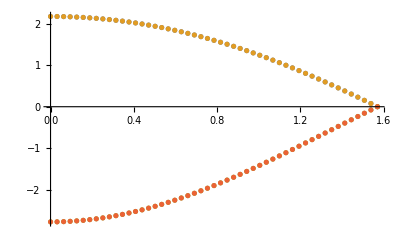

```mathematica
ListPlot[{data2D1⟦1⟧,data2D1⟦2⟧,data2D1⟦3⟧,data2D1⟦4⟧}]
```

```mathematica
mc2D1=Table[0,{i,1,div+1}];
For[i=0,i≤Pi,i=i+Pi/div,
mc2D1[[Simplify[(i)(div/(Pi))+1]]]=h[i,0];
]
u2D1=Table[0,{i,1,div+1}];
For[i=1,i≤div+1,i++,
u2D1[[i]]={Simplify[(i-1)(Pi/div)],Simplify[(i-1)(Pi/div)],Sort[Re[Eigenvalues[mc2D1⟦i⟧]],Greater]}
]
data2D1=Table[Table[{u2D1[[i]][[2]],u2D1[[i]][[3]][[j]]},{i,1,div+1}],{j,1,4}];
```

```mathematica
data2D5
```

{{{4 π,0.},{(401 π)/100,0.0314108},{(201 π)/50,0.0627905},{(403 π)/100,0.0941083},{(101 π)/25,0.125333},{(81 π)/20,0.156434},{(203 π)/50,0.187381},{(407 π)/100,0.218143},{(102 π)/25,0.24869},{(409 π)/100,0.278991},{(41 π)/10,0.309017},{(411 π)/100,0.338738},{(103 π)/25,0.368125},{(413 π)/100,0.397148},{(207 π)/50,0.425779},{(83 π)/20,0.45399},{(104 π)/25,0.481754},{(417 π)/100,0.509041},{(209 π)/50,0.535827},{(419 π)/100,0.562083},{(21 π)/5,0.587785},{(421 π)/100,0.612907},{(211 π)/50,0.637424},{(423 π)/100,0.661312},{(106 π)/25,0.684547},{(17 π)/4,0.707107},{(213 π)/50,0.728969},{(427 π)/100,0.750111},{(107 π)/25,0.770513},{(429 π)/100,0.790155},{(43 π)/10,0.809017},{(431 π)/100,0.827081},{(108 π)/25,0.844328},{(433 π)/100,0.860742},{(217 π)/50,0.876307},{(87 π)/20,0.891007},{(109 π)/25,0.904827},{(437 π)/100,0.917755},{(219 π)/50,0.929776},{(439 π)/100,0.940881},{(22 π)/5,0.951057},{(441 π)/100,0.960294},{(221 π)/50,0.968583},{(443 π)/100,0.975917},{(111 π)/25,0.982287},{(89 π)/20,0.987688},{(223 π)/50,0.992115},{(447 π)/100,0.995562},{(112 π)/25,0.998027},{(449 π)/100,0.999507},{(9 π)/2,1.},{(451 π)/100,0.999507},{(113 π)/25,0.998027},{(453 π)/100,0.995562},{(227 π)/50,0.992115},{(91 π)/20,0.987688},{(114 π)/25,0.982287},{(457 π)/100,0.975917},{(229 π)/50,0.968583},{(459 π)/100,0.960294},{(23 π)/5,0.951057},{(461 π)/100,0.940881},{(231 π)/50,0.929776},{(463 π)/100,0.917755},{(116 π)/25,0.904827},{(93 π)/20,0.891007},{(233 π)/50,0.876307},{(467 π)/100,0.860742},{(117 π)/25,0.844328},{(469 π)/100,0.827081},{(47 π)/10,0.809017},{(471 π)/100,0.790155},{(118 π)/25,0.770513},{(473 π)/100,0.750111},{(237 π)/50,0.728969},{(19 π)/4,0.707107},{(119 π)/25,0.684547},{(477 π)/100,0.661312},{(239 π)/50,0.637424},{(479 π)/100,0.612907},{(24 π)/5,0.587785},{(481 π)/100,0.562083},{(241 π)/50,0.535827},{(483 π)/100,0.509041},{(121 π)/25,0.481754},{(97 π)/20,0.45399},{(243 π)/50,0.425779},{(487 π)/100,0.397148},{(122 π)/25,0.368125},{(489 π)/100,0.338738},{(49 π)/10,0.309017},{(491 π)/100,0.278991},{(123 π)/25,0.24869},{(493 π)/100,0.218143},{(247 π)/50,0.187381},{(99 π)/20,0.156434},{(124 π)/25,0.125333},{(497 π)/100,0.0941083},{(249 π)/50,0.0627905},{(499 π)/100,0.0314108},{5 π,0.}},{{4 π,0.},{(401 π)/100,0.0314108},{(201 π)/50,0.0627905},{(403 π)/100,0.0941083},{(101 π)/25,0.125333},{(81 π)/20,0.156434},{(203 π)/50,0.187381},{(407 π)/100,0.218143},{(102 π)/25,0.24869},{(409 π)/100,0.278991},{(41 π)/10,0.309017},{(411 π)/100,0.338738},{(103 π)/25,0.368125},{(413 π)/100,0.397148},{(207 π)/50,0.425779},{(83 π)/20,0.45399},{(104 π)/25,0.481754},{(417 π)/100,0.509041},{(209 π)/50,0.535827},{(419 π)/100,0.562083},{(21 π)/5,0.587785},{(421 π)/100,0.612907},{(211 π)/50,0.637424},{(423 π)/100,0.661312},{(106 π)/25,0.684547},{(17 π)/4,0.707107},{(213 π)/50,0.728969},{(427 π)/100,0.750111},{(107 π)/25,0.770513},{(429 π)/100,0.790155},{(43 π)/10,0.809017},{(431 π)/100,0.827081},{(108 π)/25,0.844328},{(433 π)/100,0.860742},{(217 π)/50,0.876307},{(87 π)/20,0.891007},{(109 π)/25,0.904827},{(437 π)/100,0.917755},{(219 π)/50,0.929776},{(439 π)/100,0.940881},{(22 π)/5,0.951057},{(441 π)/100,0.960294},{(221 π)/50,0.968583},{(443 π)/100,0.975917},{(111 π)/25,0.982287},{(89 π)/20,0.987688},{(223 π)/50,0.992115},{(447 π)/100,0.995562},{(112 π)/25,0.998027},{(449 π)/100,0.999507},{(9 π)/2,1.},{(451 π)/100,0.999507},{(113 π)/25,0.998027},{(453 π)/100,0.995562},{(227 π)/50,0.992115},{(91 π)/20,0.987688},{(114 π)/25,0.982287},{(457 π)/100,0.975917},{(229 π)/50,0.968583},{(459 π)/100,0.960294},{(23 π)/5,0.951057},{(461 π)/100,0.940881},{(231 π)/50,0.929776},{(463 π)/100,0.917755},{(116 π)/25,0.904827},{(93 π)/20,0.891007},{(233 π)/50,0.876307},{(467 π)/100,0.860742},{(117 π)/25,0.844328},{(469 π)/100,0.827081},{(47 π)/10,0.809017},{(471 π)/100,0.790155},{(118 π)/25,0.770513},{(473 π)/100,0.750111},{(237 π)/50,0.728969},{(19 π)/4,0.707107},{(119 π)/25,0.684547},{(477 π)/100,0.661312},{(239 π)/50,0.637424},{(479 π)/100,0.612907},{(24 π)/5,0.587785},{(481 π)/100,0.562083},{(241 π)/50,0.535827},{(483 π)/100,0.509041},{(121 π)/25,0.481754},{(97 π)/20,0.45399},{(243 π)/50,0.425779},{(487 π)/100,0.397148},{(122 π)/25,0.368125},{(489 π)/100,0.338738},{(49 π)/10,0.309017},{(491 π)/100,0.278991},{(123 π)/25,0.24869},{(493 π)/100,0.218143},{(247 π)/50,0.187381},{(99 π)/20,0.156434},{(124 π)/25,0.125333},{(497 π)/100,0.0941083},{(249 π)/50,0.0627905},{(499 π)/100,0.0314108},{5 π,0.}},{{4 π,0.},{(401 π)/100,-0.0314108},{(201 π)/50,-0.0627905},{(403 π)/100,-0.0941083},{(101 π)/25,-0.125333},{(81 π)/20,-0.156434},{(203 π)/50,-0.187381},{(407 π)/100,-0.218143},{(102 π)/25,-0.24869},{(409 π)/100,-0.278991},{(41 π)/10,-0.309017},{(411 π)/100,-0.338738},{(103 π)/25,-0.368125},{(413 π)/100,-0.397148},{(207 π)/50,-0.425779},{(83 π)/20,-0.45399},{(104 π)/25,-0.481754},{(417 π)/100,-0.509041},{(209 π)/50,-0.535827},{(419 π)/100,-0.562083},{(21 π)/5,-0.587785},{(421 π)/100,-0.612907},{(211 π)/50,-0.637424},{(423 π)/100,-0.661312},{(106 π)/25,-0.684547},{(17 π)/4,-0.707107},{(213 π)/50,-0.728969},{(427 π)/100,-0.750111},{(107 π)/25,-0.770513},{(429 π)/100,-0.790155},{(43 π)/10,-0.809017},{(431 π)/100,-0.827081},{(108 π)/25,-0.844328},{(433 π)/100,-0.860742},{(217 π)/50,-0.876307},{(87 π)/20,-0.891007},{(109 π)/25,-0.904827},{(437 π)/100,-0.917755},{(219 π)/50,-0.929776},{(439 π)/100,-0.940881},{(22 π)/5,-0.951057},{(441 π)/100,-0.960294},{(221 π)/50,-0.968583},{(443 π)/100,-0.975917},{(111 π)/25,-0.982287},{(89 π)/20,-0.987688},{(223 π)/50,-0.992115},{(447 π)/100,-0.995562},{(112 π)/25,-0.998027},{(449 π)/100,-0.999507},{(9 π)/2,-1.},{(451 π)/100,-0.999507},{(113 π)/25,-0.998027},{(453 π)/100,-0.995562},{(227 π)/50,-0.992115},{(91 π)/20,-0.987688},{(114 π)/25,-0.982287},{(457 π)/100,-0.975917},{(229 π)/50,-0.968583},{(459 π)/100,-0.960294},{(23 π)/5,-0.951057},{(461 π)/100,-0.940881},{(231 π)/50,-0.929776},{(463 π)/100,-0.917755},{(116 π)/25,-0.904827},{(93 π)/20,-0.891007},{(233 π)/50,-0.876307},{(467 π)/100,-0.860742},{(117 π)/25,-0.844328},{(469 π)/100,-0.827081},{(47 π)/10,-0.809017},{(471 π)/100,-0.790155},{(118 π)/25,-0.770513},{(473 π)/100,-0.750111},{(237 π)/50,-0.728969},{(19 π)/4,-0.707107},{(119 π)/25,-0.684547},{(477 π)/100,-0.661312},{(239 π)/50,-0.637424},{(479 π)/100,-0.612907},{(24 π)/5,-0.587785},{(481 π)/100,-0.562083},{(241 π)/50,-0.535827},{(483 π)/100,-0.509041},{(121 π)/25,-0.481754},{(97 π)/20,-0.45399},{(243 π)/50,-0.425779},{(487 π)/100,-0.397148},{(122 π)/25,-0.368125},{(489 π)/100,-0.338738},{(49 π)/10,-0.309017},{(491 π)/100,-0.278991},{(123 π)/25,-0.24869},{(493 π)/100,-0.218143},{(247 π)/50,-0.187381},{(99 π)/20,-0.156434},{(124 π)/25,-0.125333},{(497 π)/100,-0.0941083},{(249 π)/50,-0.0627905},{(499 π)/100,-0.0314108},{5 π,0.}},{{4 π,0.},{(401 π)/100,-0.0314108},{(201 π)/50,-0.0627905},{(403 π)/100,-0.0941083},{(101 π)/25,-0.125333},{(81 π)/20,-0.156434},{(203 π)/50,-0.187381},{(407 π)/100,-0.218143},{(102 π)/25,-0.24869},{(409 π)/100,-0.278991},{(41 π)/10,-0.309017},{(411 π)/100,-0.338738},{(103 π)/25,-0.368125},{(413 π)/100,-0.397148},{(207 π)/50,-0.425779},{(83 π)/20,-0.45399},{(104 π)/25,-0.481754},{(417 π)/100,-0.509041},{(209 π)/50,-0.535827},{(419 π)/100,-0.562083},{(21 π)/5,-0.587785},{(421 π)/100,-0.612907},{(211 π)/50,-0.637424},{(423 π)/100,-0.661312},{(106 π)/25,-0.684547},{(17 π)/4,-0.707107},{(213 π)/50,-0.728969},{(427 π)/100,-0.750111},{(107 π)/25,-0.770513},{(429 π)/100,-0.790155},{(43 π)/10,-0.809017},{(431 π)/100,-0.827081},{(108 π)/25,-0.844328},{(433 π)/100,-0.860742},{(217 π)/50,-0.876307},{(87 π)/20,-0.891007},{(109 π)/25,-0.904827},{(437 π)/100,-0.917755},{(219 π)/50,-0.929776},{(439 π)/100,-0.940881},{(22 π)/5,-0.951057},{(441 π)/100,-0.960294},{(221 π)/50,-0.968583},{(443 π)/100,-0.975917},{(111 π)/25,-0.982287},{(89 π)/20,-0.987688},{(223 π)/50,-0.992115},{(447 π)/100,-0.995562},{(112 π)/25,-0.998027},{(449 π)/100,-0.999507},{(9 π)/2,-1.},{(451 π)/100,-0.999507},{(113 π)/25,-0.998027},{(453 π)/100,-0.995562},{(227 π)/50,-0.992115},{(91 π)/20,-0.987688},{(114 π)/25,-0.982287},{(457 π)/100,-0.975917},{(229 π)/50,-0.968583},{(459 π)/100,-0.960294},{(23 π)/5,-0.951057},{(461 π)/100,-0.940881},{(231 π)/50,-0.929776},{(463 π)/100,-0.917755},{(116 π)/25,-0.904827},{(93 π)/20,-0.891007},{(233 π)/50,-0.876307},{(467 π)/100,-0.860742},{(117 π)/25,-0.844328},{(469 π)/100,-0.827081},{(47 π)/10,-0.809017},{(471 π)/100,-0.790155},{(118 π)/25,-0.770513},{(473 π)/100,-0.750111},{(237 π)/50,-0.728969},{(19 π)/4,-0.707107},{(119 π)/25,-0.684547},{(477 π)/100,-0.661312},{(239 π)/50,-0.637424},{(479 π)/100,-0.612907},{(24 π)/5,-0.587785},{(481 π)/100,-0.562083},{(241 π)/50,-0.535827},{(483 π)/100,-0.509041},{(121 π)/25,-0.481754},{(97 π)/20,-0.45399},{(243 π)/50,-0.425779},{(487 π)/100,-0.397148},{(122 π)/25,-0.368125},{(489 π)/100,-0.338738},{(49 π)/10,-0.309017},{(491 π)/100,-0.278991},{(123 π)/25,-0.24869},{(493 π)/100,-0.218143},{(247 π)/50,-0.187381},{(99 π)/20,-0.156434},{(124 π)/25,-0.125333},{(497 π)/100,-0.0941083},{(249 π)/50,-0.0627905},{(499 π)/100,-0.0314108},{5 π,0.}}}